```mathematica
data = ResourceData["Sea Level and Temperatures Over the Last 40 Million Years"];
```

```mathematica
slvt := Transpose[QuantityMagnitude[Normal[Values[ResourceData["Sea Level and Temperatures Over the Last 40 Million Years"][{"NorthernHemisphereMeanContinentalTemperature","SeaLevel"}]]]]]
```

```mathematica
fslvt := RandomSample[Select[slvt, 0<#[[1]] && #[[1]] < 15&],1000]
```

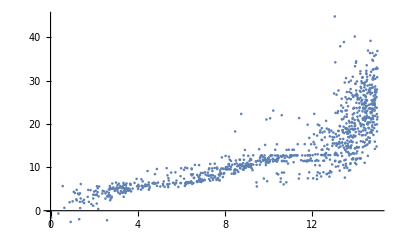

```mathematica
ListPlot[fslvt]
```

```mathematica
model = LinearModelFit[fslvt,t,t]
```

FittedModel[-2.51415+1.63811 t]

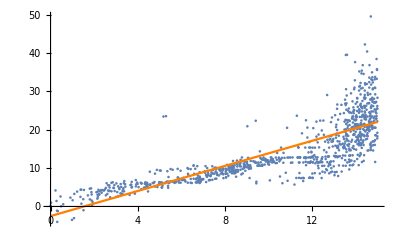

```mathematica
Show[
ListPlot[fslvt],
Plot[model[t],{t,0,15}, PlotStyle->{Orange}]]
```

```mathematica
api := APIFunction[{"t"->RepeatingElement["Number"]},(model /@#t) - 11.4&]
```

```mathematica
CloudDeploy[api, Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/objects/132a9d0d-9e3a-4d76-93b8-d92068b3d949]

```mathematica
model[8.5]
```

11.4098

```mathematica
IntegerPart[9.439105291519208]
```

9

```mathematica
model /. x->8.5
```

9.29831